# Tonks-Girardeau gas: the Bethe Ansatz solution in a random finite lattice, analytical form

```mathematica
Import["/Users/irina 1/qsu_repo/bethe_ansatz/RandomLattice.png"]
```

Import::nffil: File not found during Import.

$Failed

## One particle case

Here I define all the parameters of the system.

```mathematica
numBar=5; (* Total number of the delta barriers*)
ys = Symbol["y"<>ToString[#]]&/@Range[1,numBar] (*List of the variables (placeholders) for the positions of the barriers*)
ds=Symbol["d"<>ToString[#]]&/@Range[1,numBar](*List of the variables (placeholders) for the heights of the barriers*)
specificRules = {L->10, ℏ->1, m->1}; (*Rules to fix the length of the box L, and the ℏ/m ratio*)
$Assumptions=Element[ds, Reals]&&Element[ys, Reals]&&Element[L, Reals] &&Element[m, Reals]&& Element[ℏ, Reals]&&Element[k, Reals](*General assumptions about parameters. They are all real.*)
```

{y1,y2,y3,y4,y5}

{d1,d2,d3,d4,d5}

(d1|d2|d3|d4|d5)∈Reals&&(y1|y2|y3|y4|y5)∈Reals&&L∈Reals&&m∈Reals&&ℏ∈Reals&&k∈Reals

Here I define cyclic permutation of the barriers with Δ∈[-L, L] shift. Note that for negative Δ the effective shift is equivalent to  L+Δ shift. This is precisely what function Mod[Δ, L] is doing.

```mathematica
(* Cyclic permutation of the barrier heights *)
cyclicBarrierShiftHeights[Δ_, ys_, ds_, L_]:=Module[{shift, signs, dels, resultDs, Nb},(Nb = Length[ds];dels=Flatten[{L/2-#&/@ Reverse[ys], L}];signs=Sign[Mod[Δ,L] - dels]; shift=Floor[Total[signs + 1]/2];resultDs = Flatten[{ds[[Nb-shift+1;;Nb]],ds[[1;;Nb-shift]]}])]
(* Cyclic permutation of the barrier positions *)
cyclicBarrierShiftPos[Δ_, ys_, L_]:=Module[{Nb, resultYs},(Nb = Length[ds];resultYs = Sort[Mod[ys+Δ + L/2, L]-L/2])]
```

## The Bethe equations

Here we construct a Bethe Equation according to

-Graphics-

```mathematica
𝒯[n_, ys_, ds_]:= Module[{combs},(combs=Subsets[Range[1,Length[ys]], {n}];2^(2n)Total[Times@@(ds[[#]] m/ℏ^2)If[Length[#]>=1, Sin[k(ys[[#]][[1]]+L/2)]Sin[k(L/2-ys[[#]][[n]])], Sin[k L]]Product[Sin[k(ys[[#]][[j]]-ys[[#]][[j-1]])],{j,2,n}]&/@combs])]
𝒯[1, ys, ds];
```

```mathematica
makeBE[ys_, ds_]:=Sum[𝒯[n, ys, ds] k^(Length[ds]-n), {n, 0, Length[ds]}]==0
AbsoluteTiming[TGBE=makeBE[ys, ds];]
```

{0.005356,Null}

## The Coefficients

Here I reconstruct the coefficients and the normaliation constant accroding to

-Graphics-

```mathematica
(*n is the number of the well in which the particle is in, for 1-particle case. The coefficient we are calculating is Subscript["𝒜", {1,0,0,0,0}][{k1}], with 1 in the well number n.  ds - heights of the barriers, ys - positions of the barriers*)
makeCoef[n_, ds_, ys_]:=Module[{combs, posCombs, elems, curProd, curYP},(combs=Subsets[Range[1,n-1], n-1]; elems = Total[(Times@@(ds[[#]]*(-2 m ⅈ)/(k ℏ^2))If[Length[#]>0,(1-Exp[-ⅈ k (L + 2 ys[[#]][[1]])]), 1])Product[(1-Exp[-ⅈ 2 k (+ys[[#]][[j]]-ys[[#]][[j-1]])]), {j, 2, Length[#]}]&/@combs])];
makeCoef[2, ds, ys];
```

```mathematica
(*Real part of a coefficient*)
```

```mathematica
realPartMakeCoef[n_, ds_, ys_]:=Module[{combs, posCombs, elems, curProd, curYP},(combs=Subsets[Range[1,n-1], n-1]; elems = Total[(Times@@(ds[[#]])((-4 m)/(k ℏ^2))^Length[#] If[Length[#]>0,(-Sin[k(L/2+ys[[#]][[1]])]Cos[k(ys[[#]][[Length[#]]]+L/2)]), 1])Product[(Sin[ k (-ys[[#]][[j]]+ys[[#]][[j-1]])]), {j, 2, Length[#]}]&/@combs])];
realPartMakeCoef[2, ds, ys];
```

```mathematica
(*Imaginary part of a coefficient *)
```

```mathematica
imPartMakeCoef[n_, ds_, ys_]:=Module[{combs, posCombs, elems, curProd, curYP},(combs=Subsets[Range[1,n-1], {1,n-1}]; elems = Total[(Times@@(ds[[#]])((-4 m)/(k ℏ^2))^Length[#] If[Length[#]>0,(Sin[k(L/2+ys[[#]][[1]])]Sin[k(ys[[#]][[Length[#]]]+L/2)]), 1])Product[(Sin[ k (-ys[[#]][[j]]+ys[[#]][[j-1]])]), {j, 2, Length[#]}]&/@combs])];
imPartMakeCoef[2, {d1,d2,d3}, {y1,y2,y3}];
```

```mathematica
(* Calculate the normalization constant*)
```

```mathematica
calcNorm[ds_, ys_]:= Module[{ReA, ImA, ReA1, ImA1},(ReA1 = realPartMakeCoef[numBar+1, ds, ys]; ImA1=imPartMakeCoef[numBar+1, ds, ys];2 (ys[[1]]+L/2 + (-(Sin[k(L+2ys[[1]])]))/(2 k)) + 2 Total[(ReA =realPartMakeCoef[#, ds, ys];ImA=imPartMakeCoef[#, ds, ys]; ReA^2(ys[[#]]-ys[[#-1]] + 1/(2 k)(-(Sin[k(L+2ys[[#]])]-Sin[k (L+2ys[[#-1]])]))) + ImA^2(ys[[#]]-ys[[#-1]] - 1/(2 k)(-(Sin[k(L+2ys[[#]])]-Sin[k (L+2ys[[#-1]])]))) - ReA ImA(Cos[k(L+2ys[[#]])]-Cos[k (L+2ys[[#-1]])])/k)&/@Range[2, numBar]]+2(ReA1^2(L/2-ys[[numBar]] + (-(Sin[k 2 L]-Sin[k (L+2ys[[numBar]])]))/(2 k)) + ImA1^2(L/2-ys[[numBar]] - (-(Sin[k 2 L]-Sin[k (L+2ys[[numBar]])]))/(2 k)) - ReA1 ImA1(Cos[k 2 L]-Cos[k (L+2ys[[numBar]])])/k))]
```

## Actual solution

```mathematica
a = γ * L/(numBar-1);
y0  = -L/2+(L-(numBar-1)a)/2;
(*position of all barriers*)
randYsAllDelta=(y0+a*(#) + δ (y0+L/2))/.specificRules&/@Range[0, numBar-1]//FullSimplify;
(*randYsAllDelta=((-L/2 + L/(2(numBar)))+L/numBar(#) + δ L/(2(numBar))(**Mod[#,2]*))/.specificRules&/@Range[0, numBar-1];*)
thumorse={0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0};
(*height of the barriers*)
randDs =(2.1+0*Mod[#+0,2])&/@Range[1, numBar](* RandomReal[{0, 3}, Length[ds]]*)(*(1)&/@Range[1, numBar]*) ;
(*randDs[[{-7, -6}]] = 0;*)
(*barrier parameters etc for the bethe equation*)
(*modified version*)
randRulesAllDelta= Flatten[{ys[[#]]->randYsAllDelta[[#]],ds[[#]]->d}&/@Range[1, Length[ds]]]
allYsAllDelta=ys[[#]]->randYsAllDelta[[#]]&/@Range[1, Length[ds]];
```

{y1→-5 (γ+(-1+γ) δ),d1→d,y2→-5/2 (γ+2 (-1+γ) δ),d2→d,y3→-5 (-1+γ) δ,d3→d,y4→γ (5/2-5 δ)+5 δ,d4→d,y5→5 (γ+δ-γ δ),d5→d}

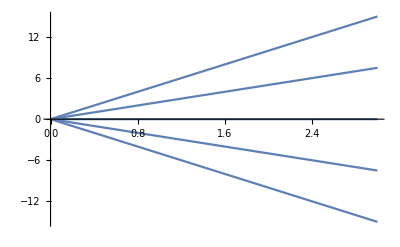

```mathematica
Plot[randYsAllDelta/.Flatten[{specificRules, δ->0}], {γ, 0, 3}]
```

```mathematica
(*cyclicBarrierShiftHeights[ -2, randYsAllDelta, ds, L/.specificRules];
Plot[cyclicBarrierShiftPos[Δ, randYsAllDelta, L/.specificRules][[1]], {Δ, -5,5}];*)
```

```mathematica
bEF = Experimental`CreateNumericalFunction[{k,g, d},{TGBE[[1]]/.Flatten[{randRulesAllDelta, specificRules}]/.{δ->0, γ->g}}, {1}, Compiled->True];
```

```mathematica
bEF[{1,0.5}]
bEF["CompiledFunction"][1,0.5]
```

Experimental`NumericalFunction[{k,g,d},{k^5 Sin[10 k]+1024 d^5 Sin[(5-5 g) k]^2 Sin[(5 g k)/2]^4+256 k (2 d^4 Sin[(5-5 g) k] Sin[(5-(5 g)/2) k] Sin[(5 g k)/2]^3+3 d^4 Sin[(5-5 g) k]^2 Sin[(5 g k)/2]^2 Sin[5 g k])+64 k^2 (2 d^3 Sin[5 k] Sin[(5-5 g) k] Sin[(5 g k)/2]^2+d^3 Sin[(5-(5 g)/2) k]^2 Sin[(5 g k)/2]^2+4 d^3 Sin[(5-5 g) k] Sin[(5-(5 g)/2) k] Sin[(5 g k)/2] Sin[5 g k]+d^3 Sin[(5-5 g) k]^2 Sin[5 g k]^2+2 d^3 Sin[(5-5 g) k]^2 Sin[(5 g k)/2] Sin[(15 g k)/2])+16 k^3 (2 d^2 Sin[5 k] Sin[(5-(5 g)/2) k] Sin[(5 g k)/2]+2 d^2 Sin[5 k] Sin[(5-5 g) k] Sin[5 g k]+d^2 Sin[(5-(5 g)/2) k]^2 Sin[5 g k]+2 d^2 Sin[(5-5 g) k] Sin[(5-(5 g)/2) k] Sin[(15 g k)/2]+d^2 Sin[(5-5 g) k]^2 Sin[10 g k]+2 d^2 Sin[(5-5 g) k] Sin[(5 g k)/2] Sin[(5+(5 g)/2) k])+4 k^4 (d Sin[5 k]^2+2 d Sin[(5-(5 g)/2) k] Sin[(5+(5 g)/2) k]+2 d Sin[(5-5 g) k] Sin[(5+5 g) k])},-NumericalFunctionData-][{1,0.5}]

CompiledFunction::cfct: Number of arguments 2 does not match the length 3 of the argument template.

CompiledFunction[…][1,0.5]

```mathematica
betheEquationsF[k_,g_, d_]=TGBE[[1]]/.Flatten[{randRulesAllDelta, specificRules}]/.{δ->0, γ->g};
bECompiled = Compile[{k, g}, betheEquationsF[k,g]]
rationalGammas = Range[0,3, 1/100];
momenta = Range[1,10,0.01];
(*butterflyValues = Flatten[Module[{g, kk},(g = rationalGammas[[#]];(kk=momenta[[#]];{g,kk,If[Abs[bEF["CompiledFunction"][kk, g][[1]]]<1^(-2), 1, 0]})&/@Range[1, Length[momenta]])&/@Range[1, Length[rationalGammas]]],1];
ListDensityPlot[butterflyValues, PlotLegends->Automatic, InterpolationOrder->0]*)
```

CompiledFunction[…]

```mathematica
(*note: use solve to get k values that solve bethe equation*)
```

```mathematica
f = betheEquationsF[k, g, d]/.{g-> 0, d-> 100}
```

2000 k^4 Sin[5 k]^2+k^5 Sin[10 k]

```mathematica
N[%]
```

{{k→0.628319},{k→1.25664},{k→1.88496},{k→2.51327},{k→3.14159},{k→3.76991},{k→4.39823},{k→5.02655},{k→5.65487},{k→6.28319},{k→6.9115},{k→7.53982},{k→8.16814},{k→8.79646},{k→9.42478},{k→0.628193},{k→1.25639},{k→1.88458},{k→2.51277},{k→3.14096},{k→3.76916},{k→4.39735},{k→5.02554},{k→5.65374},{k→6.28193},{k→6.91012},{k→7.53831},{k→8.16651},{k→8.7947},{k→9.42289}}

```mathematica
rationalGammas[[80;;90]]
```

{79/100,4/5,81/100,41/50,83/100,21/25,17/20,43/50,87/100,22/25,89/100}

```mathematica
N[%]
```

{0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89}

```mathematica
points =Flatten[Table[{k, g}/.NSolve[(bECompiled[k,g]==0)&&k > 1.0 && k <10,k, Reals, WorkingPrecision->5], {g, (numBar-1)/(numBar+1), 3, 1/100}],  1];
```

CompiledFunction::cfsa: Argument k at position 1 should be a machine-size real number.

ReplaceAll::reps: {NSolve[1024 d^5 Sin[«1»]^6+1280 d^4 k Sin[«1»]^4 Sin[Times[«2»]]+64 k^2 (Times[«4»]+Times[«4»])+16 k^3 (Times[«2»]+Times[«5»]+Times[«4»])+4 k^4 (Times[«2»]+Times[«4»]+Times[«4»])+k^5 Sin[Times[«2»]]==0&&k>1.&&k<10,k,Reals,WorkingPrecision→5]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

CompiledFunction::cfsa: Argument k at position 1 should be a machine-size real number.

$Aborted

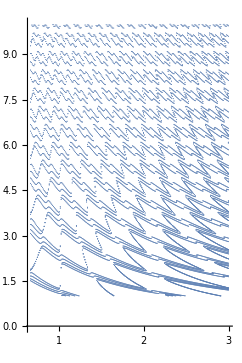

```mathematica
butterflyValues = {#[[2]], #[[1]]}&/@ points;
ListPlot[butterflyValues, PlotLegends->Automatic, InterpolationOrder->0, PlotRange->Full, AspectRatio->1.5]
```

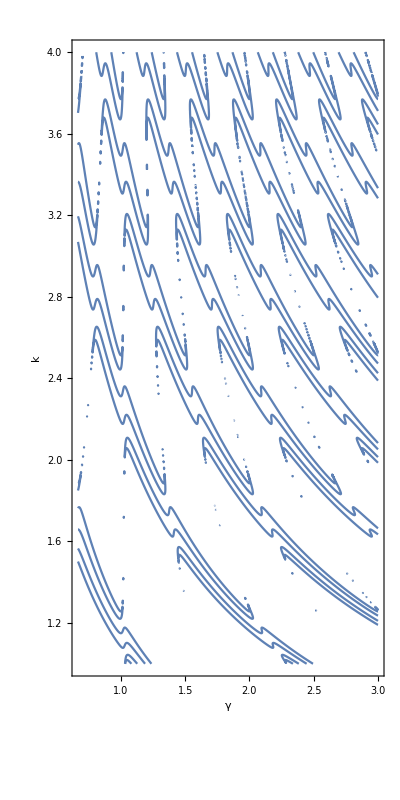

```mathematica
SetOptions[ContourPlot,BaseStyle->{FontFamily->"Times",FontSize->14}];
plotObj1=ContourPlot[{bEF["CompiledFunction"][k, γ]==0},{γ, (numBar-1)/(numBar+1),3}, {k, 1, 4}, PlotRange->Full, PlotLegends->Automatic, PlotPoints->150, FrameLabel->{"γ", "k"}, AspectRatio->2, WorkingPrecision->50, Exclusions->None ]
```

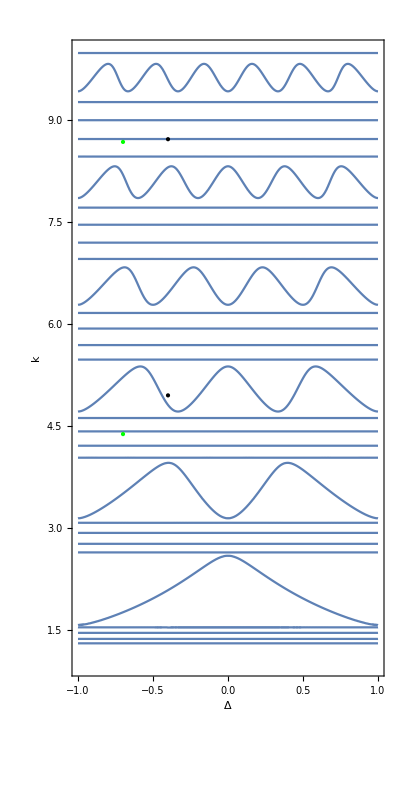

```mathematica
betheEquations=TGBE[[1]]/.Flatten[{randRulesAllDelta, specificRules}]/.{δ->Δ,γ->(numBar-1)/numBar};
SetOptions[ContourPlot,BaseStyle->{FontFamily->"Times",FontSize->14}];
plotObj1=ContourPlot[{betheEquations==0},{Δ, -1,1}, {k, 1, 10}, PlotRange->Full, PlotLegends->Automatic, PlotPoints->100, FrameLabel->{"Δ", "k"}, AspectRatio->2 , Epilog->{Thin,{Green,Point[{-0.7,8.68}],Green,Point[{-0.7,4.38}], Black, Point[{-0.4,8.72}], Black,Point[{-0.4,4.95}]}}]
(*orderedPairs=First[Cases[plotObj,x_GraphicsComplex :>  First@x,Infinity]];
orderedSqrP={#[[1]], #[[2]]^2} &/@ orderedPairs;
lineData=Cases[plotObj,x_Line :>  x,Infinity];
linesIndex = Cases[lineData,Line[x_] :>  x,Infinity];
allLines = orderedSqrP[[#]]&/@ linesIndex;
Length[orderedPairs]
Length[lineData]*)
```

```mathematica
Delta=0;
GGamma =17/20(*(numBar-1)/numBar*);
randYs=randYsAllDelta/.Flatten[{specificRules}](*Sort[RandomReal[{-L/2, L/2}/.specificRules, Length[ys]]]*)(*{3}*);
randRules =randRulesAllDelta/.Flatten[{specificRules}]
```

{y1→-5 (γ+(-1+γ) δ),d1→2.1,y2→-5/2 (γ+2 (-1+γ) δ),d2→2.1,y3→-5 (-1+γ) δ,d3→2.1,y4→γ (5/2-5 δ)+5 δ,d4→2.1,y5→5 (γ+δ-γ δ),d5→2.1}

```mathematica
(*plotObj=ContourPlot[Evaluate[{TGBE/.k->k1, TGBE/.k->k2}//.Flatten[{specificRules, δ->Delta, γ->GGamma, randRules}]], {k1, -0.1, 9}, {k2, -0.1, 5}, PlotPoints->300,PlotLegends->Automatic, FrameLabel->{"k1", "k2"}]*)
```

```mathematica
(*sampleroots=Cases[(*Normal@*)plotObj,(*Line[pts_,___]:>pts*)GraphicsComplex[pts__]:>pts,Infinity];
ListPlot[#[[1]]&/@sampleroots[[1]]]*)
```

```mathematica
initPt ={3.9};
rootPt = FindRoot[TGBE//.Flatten[{specificRules, δ->Delta,γ->GGamma, randRules}],{k, #}]&/@initPt
```

{{k→3.88354}}

```mathematica
rootPt=NSolve[(TGBE//.Flatten[{specificRules, δ->Delta,γ->GGamma, randRules}])&&k > 1.0 && k <4,k, Reals, WorkingPrecision->20]
```

{{k→1.2363594844242882204},{k→1.2976969694022173132},{k→1.3784499091496170827},{k→1.4494610932542120417},{k→2.4948244553054807473},{k→2.5963518490972821369},{k→2.7397809852715189325},{k→2.8854173840747017811},{k→3.5873702196370850548},{k→3.6061202729880719552},{k→3.8835359014057303492}}

```mathematica
(TGBE[[1]]//.Flatten[{specificRules, δ->Delta,γ->GGamma, randRules, rootPt[[#]]}])&/@Range[1,Length[rootPt]]
```

{-6.82121×10^-13,-1.13687×10^-13,8.52651×10^-14,-2.84217×10^-14,3.63798×10^-12,4.54747×10^-12,2.72848×10^-12,-9.09495×10^-13,-3.63798×10^-12,-1.81899×10^-12,2.27374×10^-12}

## The wave function

```mathematica
Acoeff[block_, P_]=Subscript["𝒜", block][P];
allBlocks[N_, barN_] := DeleteDuplicates[Flatten[Permutations[#]&/@(PadRight[#, barN+1]&/@IntegerPartitions[N, barN+1]),1]]
χ[wellN_, ds_, ys_] := Module[{ Ep}, (Ep ={k,-k}; ∑_(ne=1)^(Dimensions[Ep][[1]]) (-Exp[-ⅈ k L])^If[Refine[Sign[Ep[[ne]]],k>0]==1,0,1](makeCoef[ wellN,ds, ys]/.k->Ep[[ne]])Exp[ⅈ Ep[[ne]] x])]
Ψ[ds_,ys_, barN_] := Module[{bN, allB, N, dels, curWell, barHs, barPos,LL}, (N=1;allB=allBlocks[N, barN];
barPos=ys;
(*barPos = Flatten[{y0,ys,Symbol["y"<>ToString[barN+1]]}];LL=2 π/k Ceiling[L k/(2 π)];Total[(curWell=#;χ[curWell, ds, ys](Product[HeavisideTheta[-barPos[[i+1]]+Sign[x]Mod[Abs[x], LL]], {i, 0, curWell-1}]Product[HeavisideTheta[barPos[[i+1]]-Sign[x]Mod[Abs[x], LL]], {i, curWell,barN+1}]))&/@Range[1,barN+1]]*)
HeavisideTheta[x+L/2]HeavisideTheta[-x+L/2]Total[(curWell=#;χ[curWell, ds, ys]Product[HeavisideTheta[-barPos[[i]]+x], {i, 1, curWell-1}]Product[HeavisideTheta[barPos[[i]]-x], {i, curWell,barN}])&/@Range[1,barN+1]])]
```

```mathematica
onePartWF[x_] =Ψ[ds,ys, numBar]//.Flatten[{specificRules, δ->Delta,γ->GGamma, randRules, #}]&/@rootPt;
```

```mathematica
rootList = (k/.#)&/@rootPt
```

{1.2363594844242882204,1.2976969694022173132,1.3784499091496170827,1.4494610932542120417,2.4948244553054807473,2.5963518490972821369,2.7397809852715189325,2.8854173840747017811,3.5873702196370850548,3.6061202729880719552,3.8835359014057303492}

```mathematica
ntoplot=Range[1,Length[rootPt]](*{numBar,2*numBar}*);

Flatten[{specificRules, δ->Delta, γ->GGamma,randRules, rootPt}]
nrmSymb = calcNorm[ds, ys];
normSqr = (nrmSymb//.Flatten[{δ->Delta,γ->GGamma,{randRules},{specificRules}, {#}}])&/@rootPt;
normSqr[[ntoplot]]
(*NIntegrate[Abs[onePartWF[x][[#]]]^2/1, Evaluate[ ({x, -L/2, L/2}/.specificRules)]]&/@ntoplot*)
```

{L→10,ℏ→1,m→1,δ→0,γ→17/20,y1→-5 (γ+(-1+γ) δ),d1→2.1,y2→-5/2 (γ+2 (-1+γ) δ),d2→2.1,y3→-5 (-1+γ) δ,d3→2.1,y4→γ (5/2-5 δ)+5 δ,d4→2.1,y5→5 (γ+δ-γ δ),d5→2.1,k→1.2363594844242882204,k→1.2976969694022173132,k→1.3784499091496170827,k→1.4494610932542120417,k→2.4948244553054807473,k→2.5963518490972821369,k→2.7397809852715189325,k→2.8854173840747017811,k→3.5873702196370850548,k→3.6061202729880719552,k→3.8835359014057303492}

{1393.11,488.797,423.846,948.836,285.928,104.492,85.4543,150.351,5.8995,5.32668,21.1786}

```mathematica
TGDensity=(Total@(Abs[onePartWF[x][[#]]]^2/normSqr[[#]]&/@ntoplot)[[1;;#]])&/@ntoplot;
```

```mathematica
SinglePartDensity = Abs[onePartWF[x][[#]]]^2/normSqr[[#]]&/@ntoplot;
```

{{-17/4,{}},{-17/8,{}},{0,{}},{17/8,{}},{17/4,{}},{-5,Directive[GrayLevel[0],Thickness[Large]]},{5,Directive[GrayLevel[0],Thickness[Large]]}}

{k -> 1.2363594844242882204,k -> 1.2976969694022173132,k -> 1.3784499091496170827,k -> 1.4494610932542120417,k -> 2.4948244553054807473,k -> 2.5963518490972821369,k -> 2.7397809852715189325,k -> 2.8854173840747017811,k -> 3.5873702196370850548,k -> 3.6061202729880719552,k -> 3.8835359014057303492}

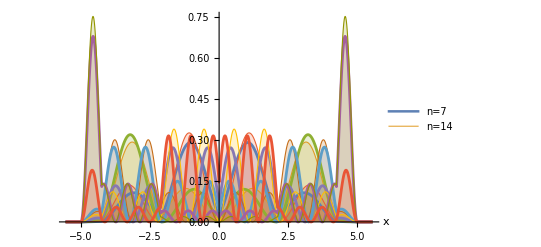

```mathematica
gridlns = Flatten[{randYs[[1;;-1]]/.{δ->Delta, γ->GGamma}, (-L/.specificRules)/2,(L/.specificRules)/2}];
glStyled=Flatten[{{gridlns[[#]], If[Mod[#,2]==1,{(*Dashed*)}, {(*Directive[Thick]*)}]}&/@ Range[1,Length[gridlns]-2],{{gridlns[[-2]], Directive[Black, Thick]}, {gridlns[[-1]], Directive[Black, Thick]}}},1]
legnd=Evaluate[ToString[#[[1]]]&/@rootPt]
SetOptions[Plot,BaseStyle->{FontFamily->"Times",FontSize->16, FontColor->Black}];
Plot[Evaluate[SinglePartDensity(*[[{6,7}]]*)],Evaluate[ ({x, -L/1.8, L/1.8}/.specificRules)],GridLines -> {glStyled, {}}, PlotRange->Full(*, PlotStyle->{Blue}*), Evaluated->True, PlotLegends->{"n=7", "n=14"}(*legnd[[ntoplot]]*), PlotPoints->150, AxesLabel->{x, ""}, PlotStyle->{Thickness[0.005], Thickness[0.002]}, Filling->Bottom, Ticks->Automatic, Exclusions->None]
```